# Homework Problem 2

-Graphics-

## a) Analytically determine the non-negative steady states (fixed points) of the model (2).

As to find a fixed point in a discrete system  needs to be fulfilled. The trivial case  = 0 can be located as the first FP. When solving the equation for a  so that the condition  is fulfilled .

```mathematica
ClearAll["Global`*"];

eq = N == (r + 1)*N/(1 + (N/K)^b);
(* Find a numerical solution for N *)
sol = NSolve[eq, N]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{N→0.},{N→1. (1000.^b r)^(1/b)}}

## b) Perform linear stability analysis and discuss how the linear stability of the non-negative steady states depends on the parameters

Lets take the derivative of the model in regard of N and check the “slope” at the found fixed points

```mathematica
ClearAll["Global`*"];
f1[n_] := (r + 1) * n / (1 + (n/K)^b)
f2[n_] = D[f1[n],n] // Simplify
```

(1000^b (1000^b-(-1+b) n^b) (1+r))/((1000^b+n^b)^2)

First we evaluate the FP N1* = 0.

```mathematica
f2[0] // Simplify
```

(1000^b (0^b+1000^b-0^b b) (1+r))/((0^b+1000^b)^2)

Further simplified one finds that the slope is .

Secondly  lets check the FP N2* =

```mathematica
f2[K*r^(1/b)] // Simplify
```

-((1+r) (-1-(r^(1/b))^b+b (r^(1/b))^b))/((1+(r^(1/b))^b)^2)

This  clears out to  , which describes the slope and therefore the stability.
Now to determine the stability we need to figure out it . In the first case the FP is unstable, in the second one stable.
For the FP1 N1* =  0, the slope of the linear approximation is , since  it follow that , we see that the system is unstable.
For the FP2 N2* = , the “eigenvalue” takes the form  . This means in terms of the stability that =1  is a critical point. As the term  can not become 0 (due to the constraints  and ), so the critical case is when  . As long as the term is smaller than 2 the FP is stable, if it is larger, the FP turns unstable.

We find a critical value for b, . In case of r = 0,  becomes 1. For values of the FP becomes stable, otherwise unstable.

## c) Analytically find all conditions on the parameters (within their ranges of validity) where a bifurcation from a stable steady state to an unstable steady state occurs.

As  described in subtask b), one finds a criticial depence of b in regard of r, . When b approaches  the stability of the FP changes.

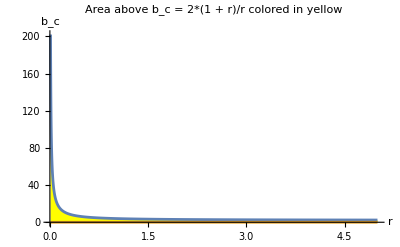

```mathematica
Plot[{2 * (1 + r)/r, 0}, {r, 0.01, 5}, 
 Filling -> {1 -> {2}}, 
 FillingStyle -> Yellow, 
 AxesLabel -> {"r", "b_c"}, 
 PlotRange -> All, 
 PlotLabel -> "Area above b_c = 2*(1 + r)/r colored in yellow"]
```

We  find  that when r goes to infinity . The stable combinations for the parameters lay in the yellow area in the plot.

## d) Investigate how the population size depends on time for the following values of the initial population size: N0 = 1, 2, 3 and 10. For each case, use the linear stability analysis performed in task b) to approximate the population dynamics in the vicinity of the unstable steady state. [Hint: treat the initial condition as a small perturbation around the unstable steady state, and plot how this perturbation, and consequently the population size, is expected to change over time according to the linear stability analysis.] Plot this approximation together with the corresponding (exact) population dynamics obtained by iterating Eq. (2). Use log-log scale for plotting to distinguish well between the different curves.

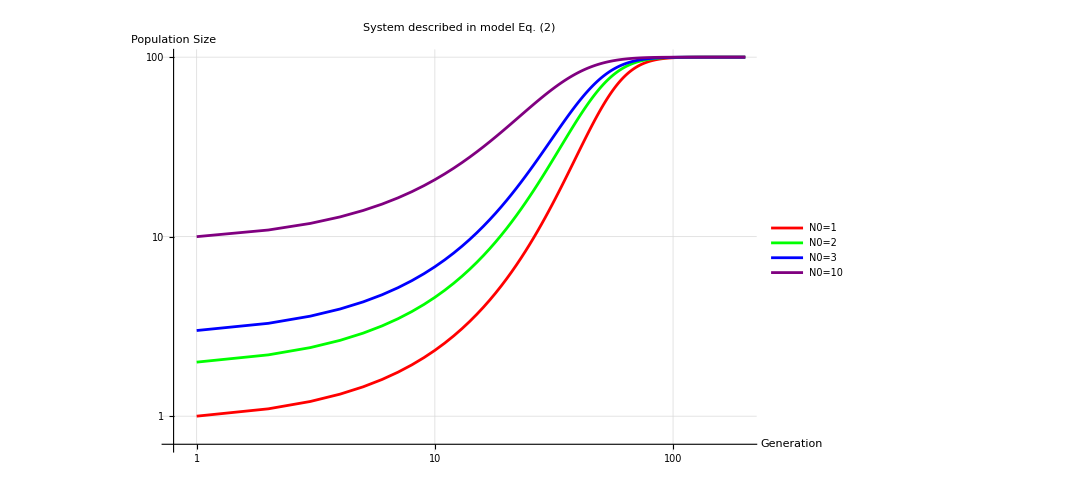

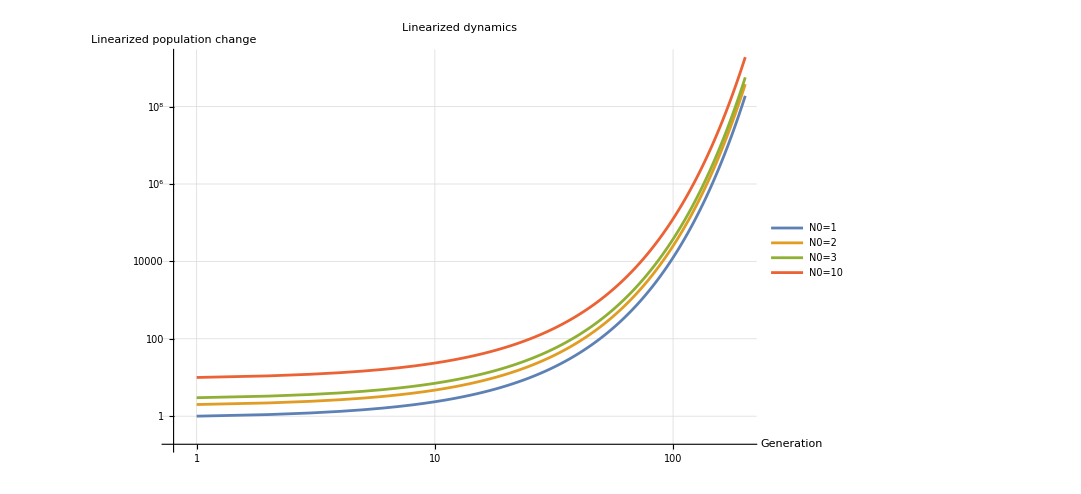

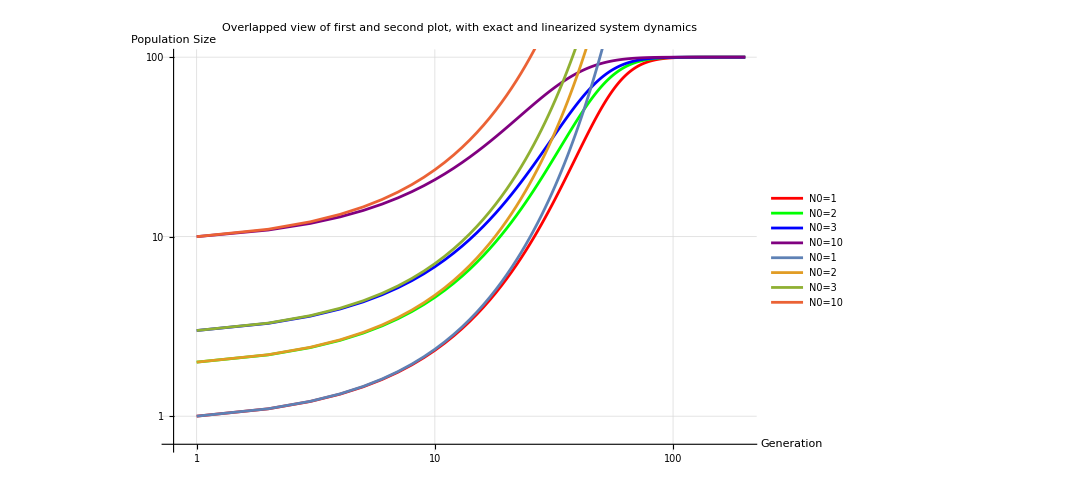

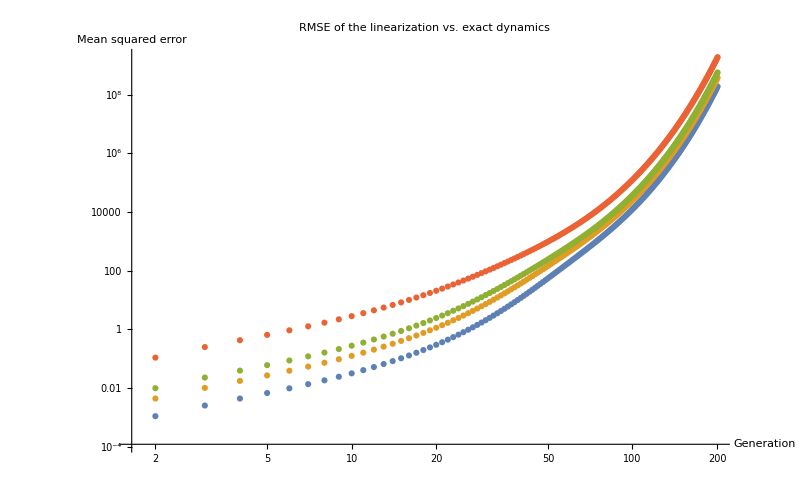

```mathematica
ClearAll["Global`*"];
K = 10^3;
r = 0.1;
b = 1;
N0values = {1,2,3,10};
unstableSteadyState = 0;
t0 = 0;
tMax = 200;

f2[n_] = n * (r+1) / (1 + (n/K)^b);
fPrime[n_] = Series[f2[n], {n, unstableSteadyState, 1}] // Normal;

(* Iteravile evaluate the function f2 for tMax generations with the four different starting values of N0*)

resultsSystem = Table[
   NestList[f2, unstableSteadyState + N0, tMax],
   {N0, N0values}
];
resultsSystem = resultsSystem;

resultsLinearized  = Table[
   NestList[fPrime, unstableSteadyState +N0, tMax],
   {N0, N0values}
];

(* Drop the 0 element of the linearized reults *) 
resultsLinearizedDropped = Map[Drop[#, 0] &, resultsLinearized];


Delta =  Sqrt[(resultsSystem - resultsLinearizedDropped) ^2]; 

 Plot1 = ListLogLogPlot[resultsSystem, PlotRange -> All, 
 PlotLegends -> {"N0=1", "N0=2", "N0=3", "N0=10"},
 Joined -> True,
 PlotLabel->"System described in model Eq. (2)",
 AxesLabel -> {"Generation", "Population Size"},
 GridLines->Automatic,
 PlotStyle -> {Red, Green, Blue, Purple},
 ImageSize -> {800, 600}]
 
 Plot2 =  ListLogLogPlot[resultsLinearizedDropped, PlotRange -> All, 
 PlotLegends -> {"N0=1", "N0=2", "N0=3", "N0=10"},
 Joined -> True,
 PlotLabel->"Linearized dynamics",
  AxesLabel -> {"Generation", "Linearized population change"},
  GridLines->Automatic,
  ImageSize -> {800, 600}]
 
 
 Show[Plot1, Plot2,
 PlotLabel -> "Overlapped view of first and second plot, with exact and linearized system dynamics",
 PlotStyle -> {Brown, Black, Yellow, Pink}
 ]
 
ListLogLogPlot[Delta,
   PlotRange -> {{Automatic, Automatic}, {Automatic, Automatic}},
   GridLines -> Automatic,
   PlotLabel -> "RMSE of the linearization vs. exact dynamics",
   ImageSize -> {800, 600},
   AxesLabel -> {"Generation", "Mean squared error"}
]
```

When doing a Taylor expansion of 1st order around the unstable fixedpoint  one finds:

When looking at this equation, its fairly obvious that the growth is not limited.

1.1 n

-Graphics-

-Graphics-

-Graphics-

-Graphics-

## e) Discuss how well the stability analysis approximates the exact dynamics. How does the initial condition influence the approximation?

As one would expect, small pertubations around an unstable fixed point do grow instead of shrink over time. Therefore our trajectories blow up over time. We see that in the early generations the approximation still holds quite well to the exact system, but then the trajectories blow up and diverge.

## f) Use linear stability analysis to approximate the dynamics in the vicinity of the stable steady state. Use initial population size N0 = N∗ +δN0, where N∗ is the value of the stable steady state and δN0 is an initial perturbation around N∗. Choose δN0 = −10, −3, −2, −1, 1, 2, 3 and 10. Proceed as follows. Starting from an initial perturbation δN0, approximate the dynamics until the system comes close to N∗ using the linear stability analysis around the stable steady state. Plot this approximation together with the exact dynamics, starting at N0. Perform the approximation for the different values of the initial perturbation δN0. How does the initial perturbation influence the approximation.

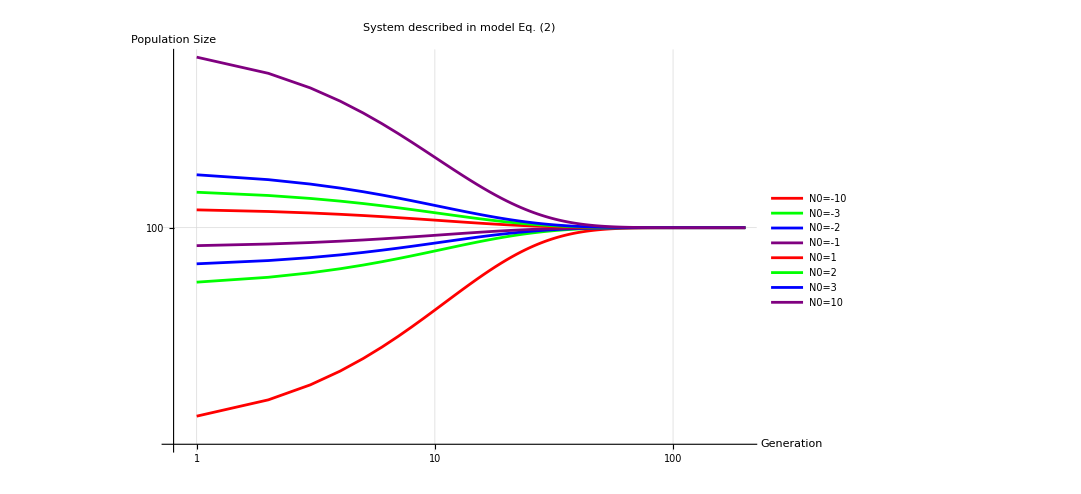

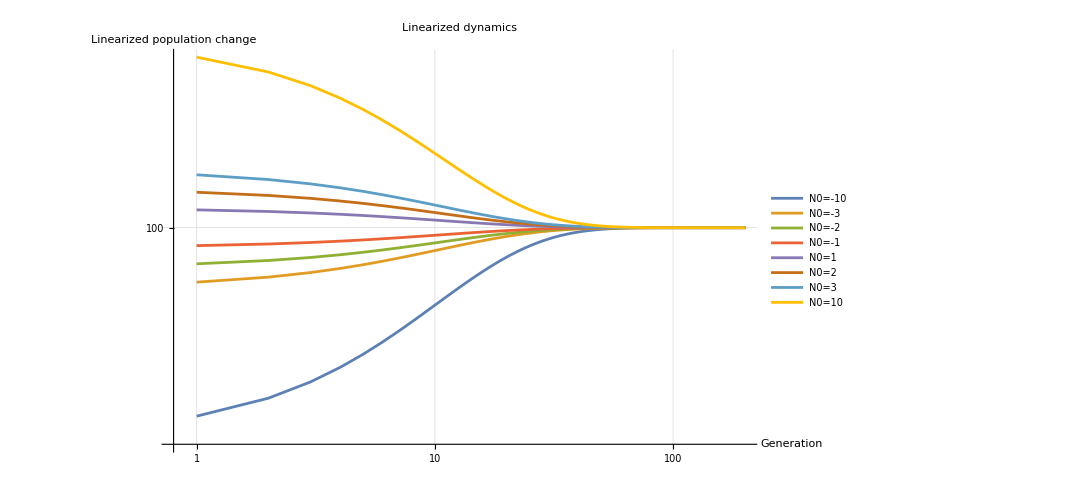

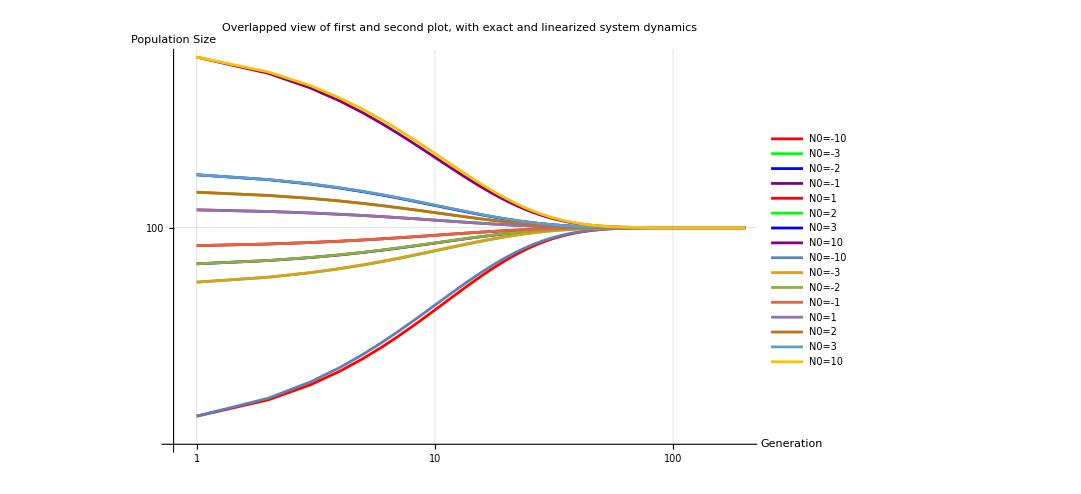

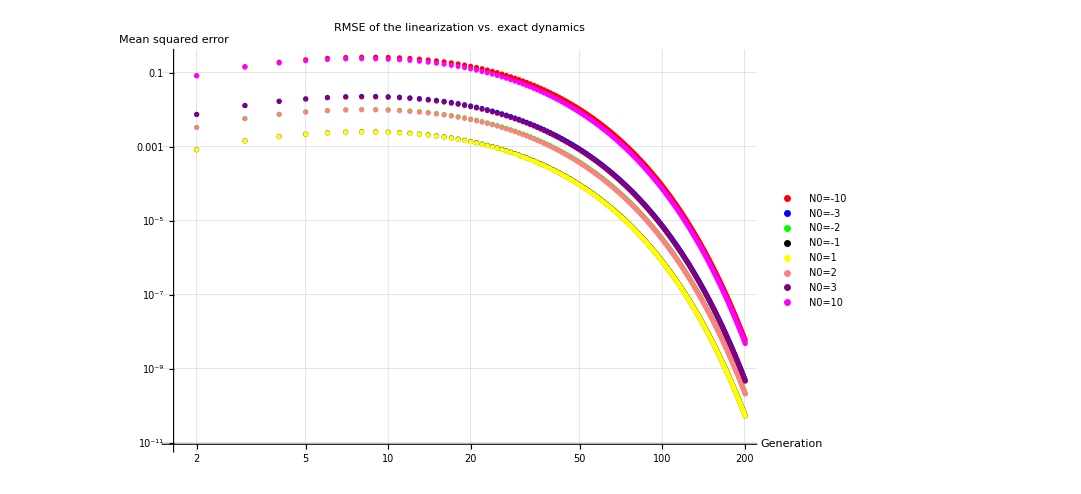

{{90.,90.9091,91.7355,92.4869,93.1699,93.7908,94.3553,94.8684,95.3349,95.759,96.1446,96.4951,96.8137,97.1034,97.3667,97.6061,97.8237,98.0216,98.2014,98.3649,98.5136,98.6487,98.7715,98.8832,98.9847,99.077,99.1609,99.2372,99.3066,99.3696,99.4269,99.479,99.5264,99.5694,99.6086,99.6442,99.6765,99.7059,99.7327,99.757,99.7791,99.7991,99.8174,99.834,99.8491,99.8628,99.8753,99.8866,99.8969,99.9063,99.9148,99.9226,99.9296,99.936,99.9418,99.9471,99.9519,99.9563,99.9603,99.9639,99.9672,99.9701,99.9729,99.9753,99.9776,99.9796,99.9815,99.9831,99.9847,99.9861,99.9873,99.9885,99.9895,99.9905,99.9914,99.9921,99.9929,99.9935,99.9941,99.9946,99.9951,99.9956,99.996,99.9963,99.9967,99.997,99.9972,99.9975,99.9977,99.9979,99.9981,99.9983,99.9984,99.9986,99.9987,99.9988,99.9989,99.999,99.9991,99.9992,99.9993,99.9993,99.9994,99.9995,99.9995,99.9995,99.9996,99.9996,99.9997,99.9997,99.9997,99.9997,99.9998,99.9998,99.9998,99.9998,99.9998,99.9999,99.9999,99.9999,99.9999,99.9999,99.9999,99.9999,99.9999,99.9999,99.9999,99.9999,99.9999,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.},{97.,97.2727,97.5207,97.7461,97.951,98.1372,98.3066,98.4605,98.6005,98.7277,98.8434,98.9485,99.0441,99.131,99.21,99.2818,99.3471,99.4065,99.4604,99.5095,99.5541,99.5946,99.6315,99.665,99.6954,99.7231,99.7483,99.7712,99.792,99.8109,99.8281,99.8437,99.8579,99.8708,99.8826,99.8932,99.903,99.9118,99.9198,99.9271,99.9337,99.9397,99.9452,99.9502,99.9547,99.9588,99.9626,99.966,99.9691,99.9719,99.9744,99.9768,99.9789,99.9808,99.9825,99.9841,99.9856,99.9869,99.9881,99.9892,99.9901,99.991,99.9919,99.9926,99.9933,99.9939,99.9944,99.9949,99.9954,99.9958,99.9962,99.9965,99.9969,99.9971,99.9974,99.9976,99.9979,99.9981,99.9982,99.9984,99.9985,99.9987,99.9988,99.9989,99.999,99.9991,99.9992,99.9992,99.9993,99.9994,99.9994,99.9995,99.9995,99.9996,99.9996,99.9996,99.9997,99.9997,99.9997,99.9998,99.9998,99.9998,99.9998,99.9998,99.9999,99.9999,99.9999,99.9999,99.9999,99.9999,99.9999,99.9999,99.9999,99.9999,99.9999,99.9999,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.},{98.,98.1818,98.3471,98.4974,98.634,98.7582,98.8711,98.9737,99.067,99.1518,99.2289,99.299,99.3627,99.4207,99.4733,99.5212,99.5647,99.6043,99.6403,99.673,99.7027,99.7297,99.7543,99.7766,99.7969,99.8154,99.8322,99.8474,99.8613,99.8739,99.8854,99.8958,99.9053,99.9139,99.9217,99.9288,99.9353,99.9412,99.9465,99.9514,99.9558,99.9598,99.9635,99.9668,99.9698,99.9726,99.9751,99.9773,99.9794,99.9813,99.983,99.9845,99.9859,99.9872,99.9884,99.9894,99.9904,99.9913,99.9921,99.9928,99.9934,99.994,99.9946,99.9951,99.9955,99.9959,99.9963,99.9966,99.9969,99.9972,99.9975,99.9977,99.9979,99.9981,99.9983,99.9984,99.9986,99.9987,99.9988,99.9989,99.999,99.9991,99.9992,99.9993,99.9993,99.9994,99.9994,99.9995,99.9995,99.9996,99.9996,99.9997,99.9997,99.9997,99.9997,99.9998,99.9998,99.9998,99.9998,99.9998,99.9999,99.9999,99.9999,99.9999,99.9999,99.9999,99.9999,99.9999,99.9999,99.9999,99.9999,99.9999,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.},{99.,99.0909,99.1736,99.2487,99.317,99.3791,99.4355,99.4868,99.5335,99.5759,99.6145,99.6495,99.6814,99.7103,99.7367,99.7606,99.7824,99.8022,99.8201,99.8365,99.8514,99.8649,99.8772,99.8883,99.8985,99.9077,99.9161,99.9237,99.9307,99.937,99.9427,99.9479,99.9526,99.9569,99.9609,99.9644,99.9677,99.9706,99.9733,99.9757,99.9779,99.9799,99.9817,99.9834,99.9849,99.9863,99.9875,99.9887,99.9897,99.9906,99.9915,99.9923,99.993,99.9936,99.9942,99.9947,99.9952,99.9956,99.996,99.9964,99.9967,99.997,99.9973,99.9975,99.9978,99.998,99.9981,99.9983,99.9985,99.9986,99.9987,99.9988,99.999,99.999,99.9991,99.9992,99.9993,99.9994,99.9994,99.9995,99.9995,99.9996,99.9996,99.9996,99.9997,99.9997,99.9997,99.9997,99.9998,99.9998,99.9998,99.9998,99.9998,99.9999,99.9999,99.9999,99.9999,99.9999,99.9999,99.9999,99.9999,99.9999,99.9999,99.9999,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.},{101.,100.909,100.826,100.751,100.683,100.621,100.564,100.513,100.467,100.424,100.386,100.35,100.319,100.29,100.263,100.239,100.218,100.198,100.18,100.164,100.149,100.135,100.123,100.112,100.102,100.092,100.084,100.076,100.069,100.063,100.057,100.052,100.047,100.043,100.039,100.036,100.032,100.029,100.027,100.024,100.022,100.02,100.018,100.017,100.015,100.014,100.012,100.011,100.01,100.009,100.009,100.008,100.007,100.006,100.006,100.005,100.005,100.004,100.004,100.004,100.003,100.003,100.003,100.002,100.002,100.002,100.002,100.002,100.002,100.001,100.001,100.001,100.001,100.001,100.001,100.001,100.001,100.001,100.001,100.001,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.},{102.,101.818,101.653,101.503,101.366,101.242,101.129,101.026,100.933,100.848,100.771,100.701,100.637,100.579,100.527,100.479,100.435,100.396,100.36,100.327,100.297,100.27,100.246,100.223,100.203,100.185,100.168,100.153,100.139,100.126,100.115,100.104,100.095,100.086,100.078,100.071,100.065,100.059,100.053,100.049,100.044,100.04,100.037,100.033,100.03,100.027,100.025,100.023,100.021,100.019,100.017,100.015,100.014,100.013,100.012,100.011,100.01,100.009,100.008,100.007,100.007,100.006,100.005,100.005,100.004,100.004,100.004,100.003,100.003,100.003,100.003,100.002,100.002,100.002,100.002,100.002,100.001,100.001,100.001,100.001,100.001,100.001,100.001,100.001,100.001,100.001,100.001,100.001,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.},{103.,102.727,102.479,102.254,102.049,101.863,101.693,101.539,101.4,101.272,101.157,101.051,100.956,100.869,100.79,100.718,100.653,100.594,100.54,100.491,100.446,100.405,100.369,100.335,100.305,100.277,100.252,100.229,100.208,100.189,100.172,100.156,100.142,100.129,100.117,100.107,100.097,100.088,100.08,100.073,100.066,100.06,100.055,100.05,100.045,100.041,100.037,100.034,100.031,100.028,100.026,100.023,100.021,100.019,100.017,100.016,100.014,100.013,100.012,100.011,100.01,100.009,100.008,100.007,100.007,100.006,100.006,100.005,100.005,100.004,100.004,100.003,100.003,100.003,100.003,100.002,100.002,100.002,100.002,100.002,100.001,100.001,100.001,100.001,100.001,100.001,100.001,100.001,100.001,100.001,100.001,100.001,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.},{110.,109.091,108.264,107.513,106.83,106.209,105.645,105.132,104.665,104.241,103.855,103.505,103.186,102.897,102.633,102.394,102.176,101.978,101.799,101.635,101.486,101.351,101.228,101.117,101.015,100.923,100.839,100.763,100.693,100.63,100.573,100.521,100.474,100.431,100.391,100.356,100.323,100.294,100.267,100.243,100.221,100.201,100.183,100.166,100.151,100.137,100.125,100.113,100.103,100.094,100.085,100.077,100.07,100.064,100.058,100.053,100.048,100.044,100.04,100.036,100.033,100.03,100.027,100.025,100.022,100.02,100.019,100.017,100.015,100.014,100.013,100.012,100.01,100.01,100.009,100.008,100.007,100.006,100.006,100.005,100.005,100.004,100.004,100.004,100.003,100.003,100.003,100.003,100.002,100.002,100.002,100.002,100.002,100.001,100.001,100.001,100.001,100.001,100.001,100.001,100.001,100.001,100.001,100.001,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.}}

```mathematica
ClearAll["Global`*"];
K = 10^3;
r = 0.1;
b = 1;
N0values = {-10,-3, -2, -1, 1,2,3,10};
unstableSteadyState = 0;
evaluatedFP2 = K * r ^(1/b);
t0 = 0;
tMax = 200;

f2[n_] = n * (r+1) / (1 + (n/K)^b);
fPrime[n_] = Series[f2[n], {n, evaluatedFP2, 1}] // Normal;

(* Iteravile evaluate the function f2 for tMax generations with the four different starting values of N0*)

resultsSystem = Table[
   NestList[f2, evaluatedFP2 + N0, tMax],
   {N0, N0values}
];
resultsSystem = resultsSystem;

resultsLinearized  = Table[
   NestList[fPrime, evaluatedFP2 +N0, tMax],
   {N0, N0values}
];

(* Drop the 0 element of the linearized reults *) 
resultsLinearizedDropped = Map[Drop[#, 0] &, resultsLinearized];
Delta =  Sqrt[(resultsSystem - resultsLinearizedDropped) ^2];

legends = "N0=" <> ToString[#] & /@ N0values;

 Plot1 = ListLogLogPlot[resultsSystem, PlotRange -> All, 
 PlotLegends -> legends,
 Joined -> True,
 PlotLabel->"System described in model Eq. (2)",
 AxesLabel -> {"Generation", "Population Size"},
 GridLines->Automatic,
 PlotStyle -> {Red, Green, Blue, Purple},
 ImageSize -> {800, 600}]
 
 Plot2 =  ListLogLogPlot[resultsLinearizedDropped, PlotRange -> All, 
 PlotLegends -> legends,
 Joined -> True,
 PlotLabel->"Linearized dynamics",
  AxesLabel -> {"Generation", "Linearized population change"},
  GridLines->Automatic,
  ImageSize -> {800, 600}]
 
 
 Show[Plot1, Plot2,
 PlotLabel -> "Overlapped view of first and second plot, with exact and linearized system dynamics",
 PlotStyle -> {Brown, Black, Yellow, Pink}
 ]
 
ListLogLogPlot[Delta,
   PlotLegends -> legends,
   PlotRange -> {{Automatic, Automatic}, {Automatic, Automatic}},
   GridLines -> Automatic,
   PlotLabel -> "RMSE of the linearization vs. exact dynamics",
   ImageSize -> {800, 600},
   AxesLabel -> {"Generation", "Mean squared error"},
   PlotStyle-> {Red, Blue, Green, Black, Yellow, Pink, Purple, Magenta}
]
```

Doing a Taylor expansion around the stable FP  one finds the following linearized dynamics:

Differently to the linearized dynamics found in subtask d) one finds a system, that has a stabilizing term (everything after the “+“ operator).
Oppositely to the approximation around the unstable FP, when linearizing around the stable FP we find that the perturbations shrink over time and get obviously “attracted”. We also find that the smaller the amplitude of the initial perturbation the smaller the approximation error.